### From hep - ph/9603205 (Appendix A1): x = (m_S/(2 m_Q))^2

```mathematica
fLight[x_]=3/2 Normal[Series[z(1+(1-z)ArcSin[1/(√z)]^2)/.{z->1/x},{x,0,8}]];
fHeavy[x_]=FullSimplify[3/2 Normal[Series[z(1+(1-z)(-1/4(Log[(1+√(1-z))/(1-√(1-z))]-I Pi)^2)),{z,0,8}]]/.{z->1/x},Assumptions->{x>1}];
fLight2[x_]:=3/2(z(1+(1-z)ArcSin[1/(√z)]^2))/.{z->1/x};
fHeavy2[x_]:=(3/2(z(1+(1-z)(-1/4(Log[-(1+√(1-z))/(1-√(1-z))])^2)))/.{z->1/x});
fAll[x_]=If[x<1,fLight[x],fHeavy[x]];
fAll2[x_]:=If[x<1,fLight2[x],fHeavy2[x]];
```

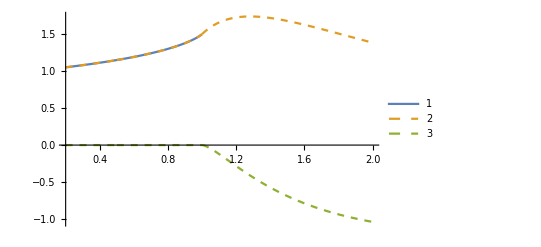

```mathematica
Plot[{fLight2[x],Re[fHeavy2[x]],Im[fHeavy2[x]]},{x,0.2,2},PlotLegends->Automatic,PlotStyle->{Thick,Dashed,Dashed}]
```

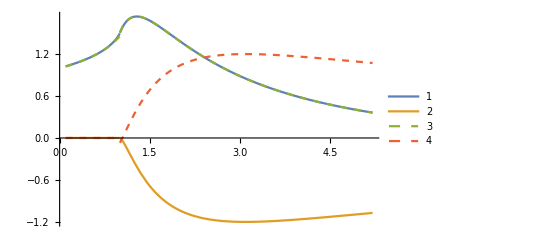

```mathematica
Plot[{Re[fAll2[x]],Im[fAll2[x]],Re[fAll[x]],Im[fAll[x]]},{x,0.1,5.2},PlotLegends->Automatic,PlotStyle->{Thick,Thick,Dashed,Dashed}]
```

```mathematica
InputForm[Expand[fLight[x]]]
```

1 + (7*x)/30 + (2*x^2)/21 + (26*x^3)/525 + (512*x^4)/17325 + (1216*x^5)/63063 + (128*x^6)/9555 + (640*x^7)/65637 + (229376*x^8)/31177575

```mathematica
InputForm[Expand[fHeavy[x]]]
```

71/(12288*x^8) + (((165*I)/28672)*Pi)/x^8 + 4003/(491520*x^7) + (((357*I)/40960)*Pi)/x^7 + 49/(4096*x^6) + (((147*I)/10240)*Pi)/x^6 + 37/(2048*x^5) + (((55*I)/2048)*Pi)/x^5 + 3/(128*x^4) + ((I/16)*Pi)/x^4 - 3/(32*x^3) + 
 (((15*I)/64)*Pi)/x^3 - (((3*I)/8)*Pi)/x^2 - (3*Pi^2)/(8*x^2) + 3/(2*x) + (3*Pi^2)/(8*x) - (165*Log[4*x])/(28672*x^8) - (357*Log[4*x])/(40960*x^7) - (147*Log[4*x])/(10240*x^6) - (55*Log[4*x])/(2048*x^5) - 
 Log[4*x]/(16*x^4) - (15*Log[4*x])/(64*x^3) + (3*Log[4*x])/(8*x^2) - (((3*I)/4)*Pi*Log[4*x])/x^2 + (((3*I)/4)*Pi*Log[4*x])/x + (3*Log[4*x]^2)/(8*x^2) - (3*Log[4*x]^2)/(8*x)

```mathematica
fHeavy[1.0]
```

1.50475-0.0705083 ⅈ

```mathematica
fHeavy[x]
```

1/(3440640 x^8)(1290240 π^2 (-1+x) x^6+7 (2840+x (4003+120 x (49+2 x (37+48 x (1-4 x+64 x^3)))))-12 ⅈ π (-1650+7 x (-357+4 x (-147+5 x (-55+32 x (-4+3 x (-5+8 x))))))+12 Log[4 x] (-1650+7 x (-357+4 x (-147+5 x (-55+32 x (-4+3 x (-5+8 (1+2 ⅈ π (-1+x)) x)))))-107520 (-1+x) x^6 Log[4 x]))

```mathematica
Expand[%]
```

71/(12288 x^8)+(165 ⅈ π)/(28672 x^8)+4003/(491520 x^7)+(357 ⅈ π)/(40960 x^7)+49/(4096 x^6)+(147 ⅈ π)/(10240 x^6)+37/(2048 x^5)+(55 ⅈ π)/(2048 x^5)+3/(128 x^4)+(ⅈ π)/(16 x^4)-3/(32 x^3)+(15 ⅈ π)/(64 x^3)-(3 ⅈ π)/(8 x^2)-(3 π^2)/(8 x^2)+3/(2 x)+(3 π^2)/(8 x)-(165 Log[4 x])/(28672 x^8)-(357 Log[4 x])/(40960 x^7)-(147 Log[4 x])/(10240 x^6)-(55 Log[4 x])/(2048 x^5)-Log[4 x]/(16 x^4)-(15 Log[4 x])/(64 x^3)+(3 Log[4 x])/(8 x^2)-(3 ⅈ π Log[4 x])/(4 x^2)+(3 ⅈ π Log[4 x])/(4 x)+(3 Log[4 x]^2)/(8 x^2)-(3 Log[4 x]^2)/(8 x)

```mathematica
Re[%]
```

-(165 π Im[1/x^8])/28672-(357 π Im[1/x^7])/40960-(147 π Im[1/x^6])/10240-(55 π Im[1/x^5])/2048-1/16 π Im[1/x^4]-15/64 π Im[1/x^3]+3/8 π Im[1/x^2]+3/4 π Im[Log[4 x]/x^2]-3/4 π Im[Log[4 x]/x]+Re[71/(12288 x^8)+4003/(491520 x^7)+49/(4096 x^6)+37/(2048 x^5)+3/(128 x^4)-3/(32 x^3)-(3 π^2)/(8 x^2)+3/(2 x)+(3 π^2)/(8 x)-(165 Log[4 x])/(28672 x^8)-(357 Log[4 x])/(40960 x^7)-(147 Log[4 x])/(10240 x^6)-(55 Log[4 x])/(2048 x^5)-Log[4 x]/(16 x^4)-(15 Log[4 x])/(64 x^3)+(3 Log[4 x])/(8 x^2)+(3 Log[4 x]^2)/(8 x^2)-(3 Log[4 x]^2)/(8 x)]

```mathematica
Simplify[%,Assumptions->{x>0}]
```

(7 (2840+4003 x+5880 x^2+8880 x^3+11520 x^4-46080 x^5-184320 π^2 x^6+184320 (4+π^2) x^7)+12 (-1650-2499 x-4116 x^2-7700 x^3-17920 x^4-67200 x^5+107520 x^6) Log[4 x]-1290240 (-1+x) x^6 Log[4 x]^2)/(3440640 x^8)

```mathematica
Expand[%]
```

71/(12288 x^8)+4003/(491520 x^7)+49/(4096 x^6)+37/(2048 x^5)+3/(128 x^4)-3/(32 x^3)-(3 π^2)/(8 x^2)+3/(2 x)+(3 π^2)/(8 x)-(165 Log[4 x])/(28672 x^8)-(357 Log[4 x])/(40960 x^7)-(147 Log[4 x])/(10240 x^6)-(55 Log[4 x])/(2048 x^5)-Log[4 x]/(16 x^4)-(15 Log[4 x])/(64 x^3)+(3 Log[4 x])/(8 x^2)+(3 Log[4 x]^2)/(8 x^2)-(3 Log[4 x]^2)/(8 x)